## Generate training data for DCNN

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs, all 4 classes)

```mathematica
RandomRuleC[n_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
netC[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
dataC[W_Integer,H_Integer,n_Integer]:=Table[RandomRuleC[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

```mathematica
netThreeCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netThreeCC1024[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 1024,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFourCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFiveCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSixCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"drop1"->DropoutLayer[0.2],"conv1"-> ConvolutionLayer[32,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSevenCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

### Functions for creating datasets (1D totalistic CAs)

#### k=3, r=1 totalistic (class 4 only)

```mathematica
gen3TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data3T2C[W_Integer,H_Integer,n_Integer]:=Table[gen3TC[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

#### k=4, r=1 totalistic (class 4 only, 1 example)

```mathematica
gen4TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data4TC[W_Integer,H_Integer,n_Integer]:=Table[gen4TC[1004600,W,H]->4,n]
```

#### k=2, r=2 totalistic (all 4 classes)

```mathematica
gen2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data2r2c4C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2C[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4C[W,H,n], data2r2c3C[W,H,n],data2r2c2C[W,H,n],data2r2c1C[W,H,n]]
```

#### k=5, r=1 totalistic (class 4 only)

```mathematica
gen5T4C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T4C[n_Integer,W_Integer,H_Integer]:=Table[gen5T4C[i,W,H]->4,{i,RandomChoice[{781130654,772514435,1151319452,309095787,880862046,973835714,779446817,345466505,535500975,793363571,1052373865,455984785,339227109,1050973846,513368817,91315820,113925357},n]}]
```

### k=5, r=1 totalistic (classes 2/3/4)

```mathematica
gen5TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T4CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->4,{i,RandomChoice[{644218533,491739943,6889640,986144962,1099816682,988971204,300829994,272622024,304100638,626595633},n]}]
data5T3CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->3,{i,RandomChoice[{889082395,541068260,807907479,816180062,650485139,643827745,753940864,871525323,351440311,83501460},n]}]
data5T2CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->2,{i,RandomChoice[{525735659,1022330944,1007796739,495633437,1036827943},n]}]
genData5TCC[W_Integer,H_Integer,n_Integer]:=Join[data5T4CC[W,H,n], data5T3CC[W,H,n],data5T2CC[W,H,n]]
```

### Generate test datasets

#### k=2, r=2 non-totalistic

```mathematica
genk2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak2r2C[W_Integer,H_Integer,n_Integer]:=Table[genk2r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=3, r=2 totalistic

```mathematica
genk3r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak3r2C[W_Integer,H_Integer,n_Integer]:=Table[genk3r2C[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

#### k=3, r=3 totalistic

```mathematica
genk3r3C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak3r3C[W_Integer,H_Integer,n_Integer]:=Table[genk3r3C[i,W,H]->i,{i,RandomChoice[Range[0,14348906],n]}]
```

#### k=4, r=1 totalistic

```mathematica
genk4r1C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak4r1C[W_Integer,H_Integer,n_Integer]:=Table[genk4r1C[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

#### k=4, r=2 totalistic

```mathematica
genk4r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak4r2C[W_Integer,H_Integer,n_Integer]:=Table[genk4r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=5, r=1 totalistic

```mathematica
gen5T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T2C[n_Integer,W_Integer,H_Integer]:=Table[gen5T2C[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

#### k=6, r=1 totalistic

```mathematica
gen6TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data6TC[n_Integer,W_Integer,H_Integer]:=Table[gen6TC[i,W,H]->i,{i,RandomInteger[2821109907455,n]}]
```

#### k=6, r=2 totalistic

```mathematica
gen6T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data6T2C[n_Integer,W_Integer,H_Integer]:=Table[gen6T2C[i,W,H]->i,{i,RandomInteger[170581728179578208255,n]}]
```

### k=7, r=1 totalistic

```mathematica
gen7TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {7,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple,8->Brown},Frame->False]]
data7TC[n_Integer,W_Integer,H_Integer]:=Table[gen7TC[i,W,H]->i,{i,RandomInteger[11398895185373142,n]}]
```

### Create training data for Network III (ECAs; k=2,r=2; k=3, r=1; k=4, r=1; k=5, r=1)

```mathematica
netECA4=netTwoCC[200,120]
```

NetChain[<>]

```mathematica
dataECA4=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC=genData2r2C[200,120,1024];
```

```mathematica
dataTotalistic3BigC=data3T2C[200,120,4096];
```

```mathematica
dataTotalistic4BigC=data4TC[200,120,4096];
```

```mathematica
dataTotalistic5BigC=data5T4C[4096,200,120];
```

```mathematica
fullTrainingBigC=Join[dataECA4,dataTotalistic2BigC,dataTotalistic3BigC,dataTotalistic4BigC,dataTotalistic5BigC];
Length[fullTrainingBigC]
RandomSample[fullTrainingBigC,20]
```

24576

{-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA4=NetTrain[netECA4,fullTrainingBigC,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","networkIV"}]
```

NetChain[<>]

```mathematica
Export["netECA6-22may-1.wlnet",netECA6,"WLNet"]
```

netECA6-22may-1.wlnet

### Training Attempt 1

```mathematica
dataECA5=dataC[200,120,2048];
dataTotalistic2BigC2=genData2r2C[200,120,256];
dataTotalistic3BigC2=data3T2C[200,120,1024];
dataTotalistic4BigC2=data4TC[200,120,1024];
dataTotalistic5BigC2=data5T4C[1024,200,120];
fullTrainingBigC2=Join[dataECA5,dataTotalistic2BigC2,dataTotalistic3BigC2,dataTotalistic4BigC2,dataTotalistic5BigC2];
Length[fullTrainingBigC2]
RandomSample[fullTrainingBigC2,20]
```

6144

{-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2}

### Training Attempt 2

```mathematica
dataECA6=dataC[200,120,8192];
dataTotalistic2BigC3=genData2r2C[200,120,512];
dataTotalistic3BigC3=data3T2C[200,120,2048];
dataTotalistic4BigC3=data4TC[200,120,2048];
dataTotalistic5BigC3=genData5TCC[200,120,1024];
fullTrainingBigC3=Join[dataECA6,dataTotalistic2BigC3,dataTotalistic3BigC3,dataTotalistic4BigC3,dataTotalistic5BigC3];
Length[fullTrainingBigC3]
RandomSample[fullTrainingBigC3,20]
```

17408

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3}

```mathematica
netECA4=NetTrain[netECA4,fullTrainingBigC3,MaxTrainingRounds->12,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Training Attempt 3

```mathematica
netECA5=netThreeCC[200,120]
```

NetChain[<>]

```mathematica
netECA5=NetTrain[netECA5,fullTrainingBigC3,MaxTrainingRounds->16,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Network VI

```mathematica
netECA6=netThreeCC1024[200,120]
```

NetChain[<>]

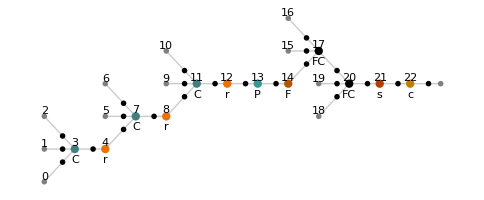

```mathematica
NetInformation[netECA6,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA6,"SummaryGraphic"]
```

-Graphics-

```mathematica
netECA6=NetTrain[netECA6,fullTrainingBigC3,MaxTrainingRounds->18,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Network VII

```mathematica
dataECA7=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC7=genData2r2C[200,120,4096];
```

```mathematica
dataTotalistic3BigC7=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC7=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC7=genData5TCC[200,120,4096];
```

```mathematica
fullTrainingBigC7=Join[dataECA7,dataTotalistic2BigC7,dataTotalistic3BigC7,dataTotalistic4BigC7,dataTotalistic5BigC7];
Length[fullTrainingBigC7]
RandomSample[fullTrainingBigC7,20]
```

38912

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2}

```mathematica
netECA7=netThreeCC1024[200,120]
```

NetChain[<>]

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA7=NetTrain[netECA7,fullTrainingBigC7,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network VII

```mathematica
testDataECABigC=dataC[200,120,1024];
testData2TBigC=genData2r2C[200,120,1024];
testData3TBigC=data3T2C[200,120,1024];
testData4TBigC=data4TC[200,120,1024];
testData5TBigC=genData5TCC[200,120,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2}

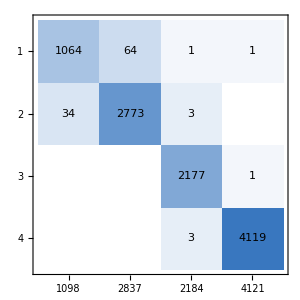
{0.989551,<|1→0.969035,2→0.977441,3→0.996795,4→0.999515|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA7, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA7[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA7[highEntBigC]]
Thread[lowEntBigC->netECA7[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→3}

{-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
testData5kr1C6=data5T2C[20,200,120];
k5r1testC6=Thread[testData5kr1C6->netECA7[Keys@testData5kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→743380617)→{2→4.05119×10^-7,4→1.},(-Graphics-→420167147)→{4→4.31548×10^-8,3→1.},(-Graphics-→60914090)→{4→0.00807698,3→0.991923},(-Graphics-→416227792)→{4→0.209166,3→0.790834},(-Graphics-→44277671)→{3→0.108628,4→0.891231},(-Graphics-→1123916113)→{3→0.352268,4→0.647732},(-Graphics-→210080263)→{3→0.0825588,4→0.917441},(-Graphics-→549817328)→{3→0.00303919,4→0.996791},(-Graphics-→14241394)→{3→9.81169×10^-9,4→1.},(-Graphics-→227347521)→{4→0.0000667955,3→0.999933},(-Graphics-→963573258)→{2→0.00405763,4→0.995942},(-Graphics-→468297088)→{4→0.0682615,3→0.931739},(-Graphics-→603744576)→{4→0.407975,3→0.592025},(-Graphics-→727654295)→{4→0.00129026,2→0.998705},(-Graphics-→546899097)→{2→0.000478121,4→0.99947},(-Graphics-→825664550)→{3→1.33098×10^-8,2→1.},(-Graphics-→702688740)→{3→1.70615×10^-6,4→0.999998},(-Graphics-→371146611)→{4→0.488173,3→0.511827},(-Graphics-→408425988)→{4→0.0549904,3→0.945009},(-Graphics-→659605814)→{4→1.87779×10^-6,2→0.999998}}

```mathematica
testData6kr1C6 = data6TC[20,200,120];
k6r1testC6=Thread[testData6kr1C6->netECA7[Keys@testData6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1041710623193)→{3→0.200591,4→0.799409},(-Graphics-→1541484819676)→{3→0.0000359852,4→0.999964},(-Graphics-→2279554396643)→{4→0.00219543,3→0.997805},(-Graphics-→696224743701)→{4→1.2178×10^-6,3→0.999999},(-Graphics-→1804464290893)→{3→0.00065873,4→0.999341},(-Graphics-→1483771507465)→{3→0.111385,4→0.888608},(-Graphics-→1191969567563)→{4→0.000208525,3→0.999791},(-Graphics-→1762402563208)→{3→0.207857,4→0.792103},(-Graphics-→1071877853786)→{4→7.61569×10^-18,2→1.},(-Graphics-→2704742708932)→{3→0.0000142801,4→0.999986},(-Graphics-→899762013116)→{4→0.00309346,2→0.995696},(-Graphics-→1652190518167)→{4→0.224451,3→0.775549},(-Graphics-→2706717337080)→{3→0.133773,4→0.866227},(-Graphics-→1753827991569)→{3→0.00240432,4→0.997596},(-Graphics-→589132365783)→{4→0.00316477,3→0.996835},(-Graphics-→1408149604868)→{4→0.00162216,3→0.998378},(-Graphics-→1560072159610)→{4→0.0103508,3→0.989649},(-Graphics-→2085943632696)→{4→0.0198733,3→0.980127},(-Graphics-→301381395692)→{2→0.00491467,4→0.995085},(-Graphics-→532232620420)→{3→0.476682,4→0.523318}}

```mathematica
test2Data6kr1C6 = data6TC[20,200,120];
k6r1test2C6=Thread[test2Data6kr1C6->netECA7[Keys@test2Data6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1399542338855)→{4→2.80487×10^-6,3→0.999997},(-Graphics-→250524360135)→{3→0.00020253,4→0.999746},(-Graphics-→549188432385)→{4→1.4749×10^-7,3→1.},(-Graphics-→1670565958943)→{3→0.453499,4→0.546501},(-Graphics-→1947156561700)→{4→0.000199657,2→0.9998},(-Graphics-→2442596135264)→{3→0.20835,4→0.79165},(-Graphics-→2813741167091)→{4→0.005064,3→0.994936},(-Graphics-→702435762432)→{4→0.161254,2→0.776976},(-Graphics-→56711608319)→{3→0.000159938,4→0.99984},(-Graphics-→954453559728)→{3→0.0436021,4→0.956398},(-Graphics-→1383877623345)→{3→0.0314444,4→0.968535},(-Graphics-→2047441890767)→{4→0.00151694,3→0.998483},(-Graphics-→2135164653304)→{4→0.199021,3→0.800921},(-Graphics-→692379794540)→{3→1.22673×10^-8,4→1.},(-Graphics-→1058788001098)→{3→7.68582×10^-7,2→0.999999},(-Graphics-→2709619897373)→{4→0.000109994,3→0.99989},(-Graphics-→2298811569801)→{4→0.0387178,3→0.961282},(-Graphics-→1843311712861)→{3→0.248157,2→0.749718},(-Graphics-→277609027910)→{3→2.53597×10^-6,4→0.999997},(-Graphics-→2413949709384)→{3→0.0000825846,4→0.999914}}

```mathematica
test3Data6kr1C6 = data6TC[20,200,120];
k6r1test3C6=Thread[test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→2572280477952)→{3→0.00244909,4→0.997551},(-Graphics-→2792470593617)→{3→1.77791×10^-6,4→0.999998},(-Graphics-→2186533635831)→{4→0.0304701,3→0.96953},(-Graphics-→780672051722)→{3→0.00222374,4→0.997775},(-Graphics-→220495815935)→{3→5.85262×10^-7,4→0.999999},(-Graphics-→1032590219492)→{4→2.08993×10^-6,3→0.999998},(-Graphics-→1619491853053)→{4→0.00772504,2→0.992274},(-Graphics-→2270970704726)→{4→0.0047662,3→0.992901},(-Graphics-→2657122596782)→{3→0.392864,4→0.607127},(-Graphics-→1154488446996)→{4→7.03027×10^-6,3→0.999993},(-Graphics-→1971033787025)→{4→0.0000152878,3→0.999985},(-Graphics-→2445830530159)→{4→0.0000522219,3→0.999948},(-Graphics-→1188506090446)→{4→6.07206×10^-6,3→0.999994},(-Graphics-→1286509461709)→{3→0.0000838736,4→0.999915},(-Graphics-→293576881330)→{2→0.000370834,4→0.999442},(-Graphics-→1374554496209)→{4→0.221928,3→0.778071},(-Graphics-→324661610660)→{4→0.208066,3→0.791934},(-Graphics-→1503631290686)→{3→0.0281068,4→0.971357},(-Graphics-→1008611736292)→{3→0.00442699,4→0.995573},(-Graphics-→1171363664378)→{3→0.00220774,4→0.997792}}

### Comparing ECA VI/VII

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA6=Import["netECA6-22may-1.wlnet"]
```

NetChain[<>]

```mathematica
netECA7=Import["netECA7 - 22_1_20_760_3.80e-2.wlnet"]
```

NetChain[<>]

```mathematica
test3Data6kr1C6 = data6TC[10,200,120];
k6r1test3C6=Thread[test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
k6r1test3C7=Thread[test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→2637743218218)→{3→0.00447142,4→0.9937},(-Graphics-→1515582137492)→{4→0.000284038,3→0.999589},(-Graphics-→259283726037)→{3→0.109871,4→0.889993},(-Graphics-→2489459019624)→{2→0.0022535,1→0.997699},(-Graphics-→1581029937445)→{3→0.000673096,4→0.999256},(-Graphics-→954067970696)→{3→0.0649123,4→0.915635},(-Graphics-→2332998281833)→{4→0.0237254,2→0.976275},(-Graphics-→1223023285351)→{4→0.163503,3→0.792209},(-Graphics-→2156538968407)→{4→0.171298,2→0.781624},(-Graphics-→727355311908)→{2→0.115246,4→0.882004}}

{(-Graphics-→2637743218218)→{3→0.0348617,4→0.965138},(-Graphics-→1515582137492)→{4→4.46249×10^-7,3→1.},(-Graphics-→259283726037)→{3→0.359188,4→0.640812},(-Graphics-→2489459019624)→{2→0.000160044,1→0.99984},(-Graphics-→1581029937445)→{4→0.144696,2→0.855304},(-Graphics-→954067970696)→{3→4.45726×10^-10,4→1.},(-Graphics-→2332998281833)→{4→6.89702×10^-6,3→0.999992},(-Graphics-→1223023285351)→{4→0.000638256,3→0.999362},(-Graphics-→2156538968407)→{3→0.0952613,4→0.904735},(-Graphics-→727355311908)→{3→0.000458633,4→0.999521}}

```mathematica
test3Data6kr1C6 = data6TC[5,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
```

{-Graphics-→{4→1.46814×10^-7,2→1.},-Graphics-→{3→0.0582502,4→0.9417},-Graphics-→{3→0.000399053,4→0.999524},-Graphics-→{3→0.0054311,4→0.994567},-Graphics-→{4→0.168105,3→0.831866}}

{-Graphics-→{4→1.03098×10^-9,2→1.},-Graphics-→{4→0.0284323,3→0.971568},-Graphics-→{3→0.146513,4→0.853487},-Graphics-→{3→0.373895,4→0.622067},-Graphics-→{4→8.59234×10^-8,3→1.}}

```mathematica
test3Data6kr1C6 = data6TC[5,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.854558},-Graphics-→{3→0.827039},-Graphics-→{2→0.99992},-Graphics-→{4→0.995722},-Graphics-→{3→0.497433}}

{-Graphics-→{4→0.985924},-Graphics-→{3→0.999643},-Graphics-→{2→1.},-Graphics-→{2→0.932116},-Graphics-→{4→0.994305}}

```mathematica
test3Data6kr1C6 = data6TC[6,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.787423},-Graphics-→{4→0.999967},-Graphics-→{4→0.798489},-Graphics-→{4→0.769221},-Graphics-→{4→0.961342},-Graphics-→{3→0.999291}}

{-Graphics-→{4→0.892224},-Graphics-→{3→0.877997},-Graphics-→{4→0.999998},-Graphics-→{3→0.997787},-Graphics-→{3→1.},-Graphics-→{4→0.856679}}

```mathematica
test3Data6kr1C6 = data6TC[5,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{2→0.99966},-Graphics-→{3→0.992687},-Graphics-→{4→0.995486},-Graphics-→{3→0.92021},-Graphics-→{3→0.676197}}

{-Graphics-→{2→0.99989},-Graphics-→{3→1.},-Graphics-→{3→0.999989},-Graphics-→{3→0.98286},-Graphics-→{3→0.556819}}

```mathematica
test3Data6kr1C6 = data6TC[6,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{4→0.935546},-Graphics-→{3→0.845159},-Graphics-→{4→0.679311},-Graphics-→{4→0.997935},-Graphics-→{3→0.664027},-Graphics-→{4→0.997733}}

{-Graphics-→{3→0.994649},-Graphics-→{3→0.997754},-Graphics-→{3→0.999999},-Graphics-→{3→0.999998},-Graphics-→{4→0.763575},-Graphics-→{4→0.999586}}

```mathematica
test3Data6kr1C6 = data6TC[6,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.990824},-Graphics-→{4→0.842102},-Graphics-→{2→0.999059},-Graphics-→{2→0.98733},-Graphics-→{3→0.983911},-Graphics-→{4→0.723212}}

{-Graphics-→{4→0.999926},-Graphics-→{3→0.922983},-Graphics-→{2→0.933794},-Graphics-→{2→1.},-Graphics-→{3→0.519157},-Graphics-→{4→1.}}

```mathematica
test3Data6kr1C6 = data6TC[6,200,120];
Thread[Keys@test3Data6kr1C6->netECA6[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.865693},-Graphics-→{3→0.908232},-Graphics-→{3→0.995335},-Graphics-→{3→0.50184},-Graphics-→{4→0.837078},-Graphics-→{4→0.7339}}

{-Graphics-→{3→0.999923},-Graphics-→{3→0.939342},-Graphics-→{4→0.997921},-Graphics-→{3→0.999995},-Graphics-→{3→1.},-Graphics-→{2→0.784849}}

```mathematica
test3Data5kr1C6 = data5T2C[6,200,120];
Thread[Keys@test3Data5kr1C6->netECA6[Keys@test3Data5kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data5kr1C6->netECA7[Keys@test3Data5kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{2→0.570335},-Graphics-→{3→0.996731},-Graphics-→{3→0.985458},-Graphics-→{3→0.984132},-Graphics-→{4→0.982008},-Graphics-→{1→0.990516}}

{-Graphics-→{3→0.999998},-Graphics-→{3→0.999303},-Graphics-→{4→0.999837},-Graphics-→{3→1.},-Graphics-→{3→0.994166},-Graphics-→{1→0.9571}}

```mathematica
test3Data7kr1C6 = data7TC[6,200,120];
Thread[Keys@test3Data7kr1C6->netECA6[Keys@test3Data7kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data7kr1C6->netECA7[Keys@test3Data7kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.729128},-Graphics-→{3→0.998874},-Graphics-→{2→0.995744},-Graphics-→{4→0.99459},-Graphics-→{3→0.993966},-Graphics-→{3→0.731632}}

{-Graphics-→{4→0.997001},-Graphics-→{2→0.998874},-Graphics-→{2→0.999901},-Graphics-→{3→0.99999},-Graphics-→{4→0.999942},-Graphics-→{3→0.998057}}

```mathematica
test3Data7kr1C6 = data7TC[6,200,120];
Thread[Keys@test3Data7kr1C6->netECA6[Keys@test3Data7kr1C6,{"TopProbabilities",1}]]
Thread[Keys@test3Data7kr1C6->netECA7[Keys@test3Data7kr1C6,{"TopProbabilities",1}]]
```

{-Graphics-→{4→0.64639},-Graphics-→{2→0.996522},-Graphics-→{4→0.961538},-Graphics-→{3→0.999322},-Graphics-→{2→0.998999},-Graphics-→{3→0.999985}}

{-Graphics-→{4→0.99928},-Graphics-→{4→0.926368},-Graphics-→{3→0.999999},-Graphics-→{3→0.99994},-Graphics-→{2→1.},-Graphics-→{3→0.997977}}

### Network VIII

```mathematica
dataECA8=dataC[150,150,8192];
```

```mathematica
dataTotalistic2BigC8=genData2r2C[150,150,4096];
```

```mathematica
dataTotalistic3BigC8=data3T2C[150,150,1024];
```

```mathematica
dataTotalistic4BigC8=data4TC[150,150,1024];
```

```mathematica
dataTotalistic5BigC8=genData5TCC[150,150,4096];
```

```mathematica
fullTrainingBigC8=Join[dataECA8,dataTotalistic2BigC8,dataTotalistic3BigC8,dataTotalistic4BigC8,dataTotalistic5BigC8];
```

```mathematica
Length[fullTrainingBigC8]
RandomSample[fullTrainingBigC8,20]
```

38912

{-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→1}

```mathematica
netECA8=netThreeCC1024[150,150]
```

NetChain[<>]

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA8=NetTrain[netECA8,fullTrainingBigC8,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network VIII

```mathematica
testDataECABigC=dataC[150,150,1024];
testData2TBigC=genData2r2C[150,150,1024];
testData3TBigC=data3T2C[150,150,1024];
testData4TBigC=data4TC[150,150,1024];
testData5TBigC=genData5TCC[150,150,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4}

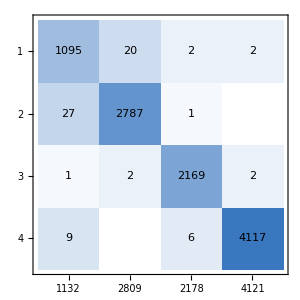
{0.992969,<|1→0.967314,2→0.992168,3→0.995868,4→0.999029|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA8, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA8[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA8[highEntBigC]]
Thread[lowEntBigC->netECA8[lowEntBigC]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3}

```mathematica
testDatak5r1C8=data5T2C[20,150,150];
k5r1testC8=Thread[testDatak5r1C8->netECA8[Keys@testDatak5r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→351576556)→{3→0.00229393,2→0.99759},(-Graphics-→282743455)→{4→0.000314574,3→0.999685},(-Graphics-→1104975539)→{4→0.0115304,3→0.988441},(-Graphics-→9756314)→{2→0.0211805,3→0.97881},(-Graphics-→258637104)→{4→0.0564866,3→0.943513},(-Graphics-→460506861)→{4→8.89447×10^-12,3→1.},(-Graphics-→1058803988)→{3→0.0235174,4→0.976483},(-Graphics-→40089852)→{3→0.000167637,4→0.999832},(-Graphics-→684452557)→{3→0.00869475,4→0.9913},(-Graphics-→267988422)→{4→0.16938,3→0.828219},(-Graphics-→1011449557)→{4→0.00685299,3→0.992847},(-Graphics-→29897960)→{3→4.48256×10^-10,4→1.},(-Graphics-→155874880)→{3→0.260244,2→0.739487},(-Graphics-→998880469)→{2→0.0447028,4→0.955125},(-Graphics-→820788605)→{3→0.000069524,4→0.999931},(-Graphics-→317899467)→{4→0.00138674,3→0.998613},(-Graphics-→336374761)→{3→0.0000280633,4→0.999972},(-Graphics-→538637563)→{4→0.0000866983,3→0.999913},(-Graphics-→134035441)→{3→1.59704×10^-8,2→1.},(-Graphics-→630627041)→{3→4.50346×10^-7,4→0.999999}}

```mathematica
testDatak6r1C8=data6TC[20,150,150];
k6r1testC8=Thread[testDatak6r1C8->netECA8[Keys@testDatak6r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→946778045702)→{4→0.00131997,2→0.998679},(-Graphics-→712191474379)→{4→0.0000183836,3→0.999982},(-Graphics-→1031607472117)→{4→1.25059×10^-8,3→1.},(-Graphics-→2027177136526)→{4→0.000509776,3→0.99949},(-Graphics-→2685487977836)→{4→0.0029637,2→0.997032},(-Graphics-→985932585038)→{4→0.000858136,3→0.999142},(-Graphics-→2690185048496)→{4→2.57655×10^-7,3→1.},(-Graphics-→36219934832)→{4→0.0397477,3→0.937959},(-Graphics-→2389241801724)→{3→0.343043,4→0.656957},(-Graphics-→1864250050050)→{3→0.485053,4→0.514931},(-Graphics-→41902188403)→{4→0.000719907,3→0.999279},(-Graphics-→585874950116)→{4→7.00336×10^-6,3→0.999993},(-Graphics-→1488894755068)→{2→2.2893×10^-8,3→1.},(-Graphics-→2317458769549)→{4→0.00590224,3→0.994096},(-Graphics-→1762606164482)→{2→0.139857,3→0.860126},(-Graphics-→2421140406120)→{4→0.441859,3→0.558141},(-Graphics-→1893422336010)→{4→0.00473302,3→0.995267},(-Graphics-→2684305769842)→{3→0.0000106101,4→0.999989},(-Graphics-→1778774599179)→{4→1.50963×10^-6,2→0.999998},(-Graphics-→2069930378941)→{3→0.0331192,4→0.966881}}

```mathematica
testDatak7r1C8=data7TC[10,150,150];
k7r1testC8=Thread[testDatak7r1C8->netECA8[Keys@testDatak7r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→555706238130239)→{1→0.000121927,2→0.999863},(-Graphics-→10071225612238266)→{4→0.485187,3→0.513807},(-Graphics-→7466826532023477)→{4→0.0716082,3→0.928392},(-Graphics-→2751312505446359)→{4→0.00110769,3→0.998892},(-Graphics-→2755723490887057)→{3→0.0000438102,4→0.999956},(-Graphics-→5035207760927362)→{4→9.30312×10^-8,3→1.},(-Graphics-→4091337242341062)→{4→0.00842218,3→0.991578},(-Graphics-→2204298304429431)→{3→0.000226268,4→0.999774},(-Graphics-→6055874584949208)→{4→2.98641×10^-8,2→1.},(-Graphics-→253516694342638)→{3→0.279442,4→0.720558}}

### Network IX - Larger convolution layers

```mathematica
netECA9=netFourCC512[200,120]
```

NetChain[<>]

### Generate training data - Network IX

```mathematica
dataECA9=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC9=genData2r2C[200,120,4096];
```

```mathematica
dataTotalistic3BigC9=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC9=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC9=genData5TCC[200,120,4096];
```

```mathematica
fullTrainingBigC9=Join[dataECA9,dataTotalistic2BigC9,dataTotalistic3BigC9,dataTotalistic4BigC9,dataTotalistic5BigC9];
Length[fullTrainingBigC9]
RandomSample[fullTrainingBigC9,20]
```

38912

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA9=NetTrain[netECA9,fullTrainingBigC9,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network IX

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA9=Import["netECA9.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[200,120,1024];
testData2TBigC=genData2r2C[200,120,1024];
testData3TBigC=data3T2C[200,120,1024];
testData4TBigC=data4TC[200,120,1024];
testData5TBigC=genData5TCC[200,120,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4}

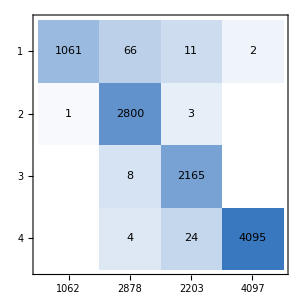
{0.988379,<|1→0.999058,2→0.972898,3→0.982751,4→0.999512|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA9, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA9[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA9[highEntBigC]]
Thread[lowEntBigC->netECA9[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→1}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
testDatak5r1C8=data5T2C[20,200,120];
k5r1testC8=Thread[testDatak5r1C8->netECA9[Keys@testDatak5r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→419078801)→{3→0.008801,4→0.991175},(-Graphics-→256576970)→{3→0.000475487,4→0.999524},(-Graphics-→1102330429)→{4→0.0580904,2→0.888368},(-Graphics-→735717182)→{2→0.000981154,4→0.998409},(-Graphics-→238308060)→{4→0.00704191,3→0.992958},(-Graphics-→270522225)→{3→0.000187586,4→0.999806},(-Graphics-→1144776786)→{4→0.0342381,3→0.965762},(-Graphics-→292920642)→{2→0.00437923,4→0.995264},(-Graphics-→904602106)→{4→0.0000979527,3→0.999902},(-Graphics-→666738617)→{4→1.65474×10^-7,2→1.},(-Graphics-→392276186)→{3→0.0759355,4→0.923805},(-Graphics-→14286760)→{4→0.316019,3→0.683981},(-Graphics-→217751619)→{2→0.0289273,4→0.96783},(-Graphics-→1044632971)→{4→7.82813×10^-8,2→1.},(-Graphics-→1197872641)→{2→0.0203652,4→0.978858},(-Graphics-→448824909)→{1→0.000157686,2→0.999841},(-Graphics-→757182767)→{4→0.000933086,3→0.999067},(-Graphics-→1136986245)→{3→0.0914631,4→0.864375},(-Graphics-→313883557)→{2→0.0827002,4→0.9173},(-Graphics-→373584230)→{4→0.0000677493,2→0.999886}}

```mathematica
testDatak6r1C8=data6TC[20,200,120];
k6r1testC8=Thread[testDatak6r1C8->netECA9[Keys@testDatak6r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→534002254660)→{4→0.000336522,3→0.999663},(-Graphics-→2333512590481)→{4→0.00864362,3→0.991356},(-Graphics-→2629973141916)→{4→0.0000400532,3→0.99996},(-Graphics-→617265091034)→{4→3.79297×10^-7,3→1.},(-Graphics-→1848061823147)→{3→0.0103179,2→0.986171},(-Graphics-→1697242636623)→{2→0.286359,3→0.515988},(-Graphics-→1301321021200)→{3→0.406782,2→0.593216},(-Graphics-→581694260878)→{4→0.00145986,3→0.998537},(-Graphics-→2786118083386)→{4→3.28543×10^-7,2→1.},(-Graphics-→1060973236586)→{4→0.347664,2→0.645546},(-Graphics-→2200328156353)→{4→0.445717,2→0.546813},(-Graphics-→576364337513)→{4→0.0338229,3→0.966158},(-Graphics-→617596858042)→{4→0.0342451,3→0.965755},(-Graphics-→623546534049)→{4→0.00492003,3→0.99508},(-Graphics-→2048169906314)→{2→0.00471489,3→0.994787},(-Graphics-→2207291229581)→{3→0.0163956,4→0.983603},(-Graphics-→204038788085)→{4→0.0258552,2→0.951902},(-Graphics-→2628924259621)→{4→0.0529741,2→0.947025},(-Graphics-→154862062413)→{4→0.000271993,3→0.999728},(-Graphics-→1797191571706)→{4→0.0095733,2→0.990111}}

### Generate training data - Network X

```mathematica
netECA10=netFiveCC512[200,120]
```

NetChain[<>]

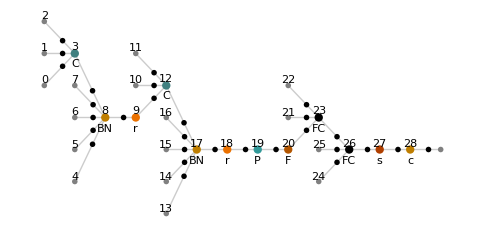

```mathematica
NetInformation[netECA10,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA10,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA10=dataC[200,120,4096];
```

```mathematica
dataTotalistic2BigC10=genData2r2C[200,120,1024];
```

```mathematica
dataTotalistic3BigC10=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC10=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC10=genData5TCC[200,120,2048];
```

```mathematica
fullTrainingBigC10=Join[dataECA10,dataTotalistic2BigC10,dataTotalistic3BigC10,dataTotalistic4BigC10,dataTotalistic5BigC10];
Length[fullTrainingBigC10]
RandomSample[fullTrainingBigC10,20]
```

16384

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA9=NetTrain[netECA9,fullTrainingBigC10,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

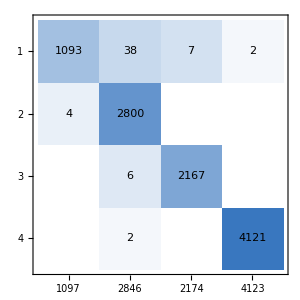
{0.994238,<|1→0.996354,2→0.983837,3→0.99678,4→0.999515|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA9, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA9[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA9[highEntBigC]]
Thread[lowEntBigC->netECA9[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→4}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

```mathematica
testDatak5r1C8=data5T2C[20,200,120];
k5r1testC8=Thread[testDatak5r1C8->netECA9[Keys@testDatak5r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→663279485)→{4→0.0373018,2→0.962686},(-Graphics-→309950342)→{4→0.372701,3→0.584165},(-Graphics-→1098198433)→{3→0.000955167,2→0.998937},(-Graphics-→542956878)→{3→0.112692,4→0.887267},(-Graphics-→1219798072)→{4→3.49623×10^-7,2→1.},(-Graphics-→981814127)→{4→0.268443,3→0.73154},(-Graphics-→471052134)→{4→0.017656,3→0.982295},(-Graphics-→877901364)→{3→0.0543509,2→0.939094},(-Graphics-→526461745)→{3→0.0700762,4→0.929891},(-Graphics-→2716778)→{4→0.00550199,3→0.994496},(-Graphics-→1032910328)→{4→0.414249,2→0.584544},(-Graphics-→841672200)→{3→0.299338,4→0.700471},(-Graphics-→765505894)→{4→0.000484491,3→0.999473},(-Graphics-→87115440)→{3→0.0504378,4→0.949526},(-Graphics-→866778321)→{3→0.000616316,2→0.999363},(-Graphics-→999068157)→{4→0.0375352,3→0.944567},(-Graphics-→396307561)→{3→0.0821956,4→0.917804},(-Graphics-→297302518)→{3→0.000210799,4→0.999729},(-Graphics-→842404440)→{3→0.115149,4→0.88187},(-Graphics-→1084920855)→{3→0.00591815,4→0.993973}}

```mathematica
testDatak6r1C8=data6TC[20,200,120];
k6r1testC8=Thread[testDatak6r1C8->netECA9[Keys@testDatak6r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→127030796737)→{4→0.00907109,3→0.990928},(-Graphics-→2406989042468)→{3→0.00176187,4→0.998228},(-Graphics-→280108299589)→{4→0.0128788,3→0.97718},(-Graphics-→1545271898392)→{3→0.00271368,2→0.997173},(-Graphics-→2781144163302)→{4→0.289733,3→0.708693},(-Graphics-→1408964747150)→{3→0.19664,4→0.802924},(-Graphics-→2634245657302)→{3→0.246877,4→0.753122},(-Graphics-→2793166743541)→{4→0.41045,3→0.58794},(-Graphics-→2776384357392)→{2→0.00285658,3→0.995654},(-Graphics-→1598677052390)→{2→0.0405571,3→0.958829},(-Graphics-→72961186085)→{4→0.000160832,3→0.999808},(-Graphics-→1669735251832)→{4→0.00330084,3→0.996699},(-Graphics-→1688594658452)→{3→0.380501,2→0.562787},(-Graphics-→154828230936)→{4→0.000512702,3→0.999486},(-Graphics-→1925079852608)→{4→0.000606216,3→0.999392},(-Graphics-→1787265141201)→{4→0.152672,3→0.847328},(-Graphics-→1389774074148)→{2→0.0283011,3→0.965982},(-Graphics-→2569366559450)→{3→0.368407,4→0.631585},(-Graphics-→180212074433)→{4→2.79498×10^-7,2→1.},(-Graphics-→1686228872586)→{4→0.000699905,3→0.9993}}

```mathematica
netECA10=NetTrain[netECA10,fullTrainingBigC10,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA10[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA10[highEntBigC]]
Thread[lowEntBigC->netECA10[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4}

```mathematica
testDatak5r1C8=data5T2C[20,200,120];
k5r1testC8=Thread[testDatak5r1C8->netECA10[Keys@testDatak5r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→234177331)→{4→0.0027247,3→0.997171},(-Graphics-→163091683)→{3→0.309143,4→0.689484},(-Graphics-→820777175)→{3→0.429028,4→0.570481},(-Graphics-→434908686)→{4→0.221366,3→0.778604},(-Graphics-→208591409)→{2→0.27933,3→0.720222},(-Graphics-→30383292)→{4→0.051772,3→0.948044},(-Graphics-→279447415)→{4→0.295444,3→0.704541},(-Graphics-→732408716)→{3→0.0194357,4→0.980336},(-Graphics-→613358985)→{3→0.10192,4→0.898067},(-Graphics-→534048034)→{2→0.00115542,3→0.998755},(-Graphics-→943459686)→{2→0.0179644,4→0.976299},(-Graphics-→118563078)→{3→0.00465445,4→0.995344},(-Graphics-→507641338)→{3→0.00266478,4→0.9973},(-Graphics-→111220500)→{3→0.296292,4→0.703701},(-Graphics-→2836489)→{4→0.443228,3→0.553256},(-Graphics-→779819664)→{4→0.315278,3→0.684535},(-Graphics-→52498762)→{2→0.315659,4→0.652134},(-Graphics-→47181713)→{4→0.037086,2→0.962374},(-Graphics-→382071264)→{4→0.00268784,3→0.997309},(-Graphics-→149909424)→{4→0.0786608,3→0.921275}}

```mathematica
testDatak6r1C8=data6TC[20,200,120];
k6r1testC8=Thread[testDatak6r1C8->netECA10[Keys@testDatak6r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→1131803027394)→{4→0.00124019,3→0.998749},(-Graphics-→1526913747530)→{3→0.161495,4→0.838503},(-Graphics-→1269085467336)→{3→0.268945,4→0.731055},(-Graphics-→1587342720816)→{4→0.234412,3→0.764784},(-Graphics-→1497161592564)→{4→0.00279246,3→0.995272},(-Graphics-→978035544046)→{3→0.264913,4→0.735066},(-Graphics-→1286358203238)→{4→0.0557109,3→0.908895},(-Graphics-→2513953203308)→{3→0.474554,4→0.524977},(-Graphics-→2737475691151)→{2→0.000407316,3→0.999409},(-Graphics-→1642355959683)→{3→0.313141,4→0.676289},(-Graphics-→2588314714256)→{3→0.299479,4→0.700034},(-Graphics-→2062214586403)→{3→0.0654688,4→0.934483},(-Graphics-→41674368132)→{3→0.0554872,4→0.944381},(-Graphics-→1540341049221)→{2→0.000661049,3→0.999304},(-Graphics-→2205257602478)→{3→0.198787,4→0.798422},(-Graphics-→1495901966623)→{3→0.156393,4→0.843297},(-Graphics-→2658911658304)→{4→0.336581,3→0.663411},(-Graphics-→1423543550537)→{4→0.00494719,3→0.994835},(-Graphics-→981040926186)→{3→0.0198643,4→0.980131},(-Graphics-→1289555460711)→{4→0.134275,3→0.865115}}

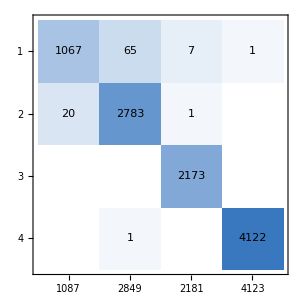
{0.990723,<|1→0.981601,2→0.976834,3→0.996332,4→0.999757|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA10, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
test3Data5kr1C10 = data5T2C[8,200,120];
Thread[Keys@test3Data5kr1C10->netECA10[Keys@test3Data5kr1C10,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.528599},-Graphics-→{4→0.974056},-Graphics-→{3→0.61017},-Graphics-→{4→0.87776},-Graphics-→{3→0.70476},-Graphics-→{1→0.748537},-Graphics-→{4→0.680216},-Graphics-→{3→0.85947}}

```mathematica
test4Data7kr1C10 = data7TC[8,200,120];
Thread[test4Data7kr1C10->netECA10[Keys@test4Data7kr1C10,{"TopProbabilities",1}]]
```

{(-Graphics-→8823913694494635)→{3→0.994297},(-Graphics-→11279996571927052)→{4→0.615814},(-Graphics-→9401097035811122)→{3→0.991581},(-Graphics-→3631971980939595)→{4→0.687827},(-Graphics-→7952036094060914)→{4→0.999626},(-Graphics-→8576162977214953)→{4→0.855862},(-Graphics-→11134668318911378)→{4→0.95093},(-Graphics-→11023371115929734)→{3→0.502334}}

```mathematica
test4Data7kr1C10 = data7TC[8,200,120];
Thread[test4Data7kr1C10->netECA10[Keys@test4Data7kr1C10,{"TopProbabilities",2}]]
```

{(-Graphics-→1099067424359500)→{4→0.0134163,3→0.98658},(-Graphics-→8043911359130963)→{4→0.258575,3→0.740435},(-Graphics-→2040932928026893)→{4→0.00972185,3→0.990256},(-Graphics-→6398988474619710)→{4→0.0101518,3→0.988888},(-Graphics-→3794540571144328)→{4→0.185737,3→0.814233},(-Graphics-→6030384314236780)→{4→0.113983,3→0.886004},(-Graphics-→9427040564525255)→{4→0.000585684,3→0.999373},(-Graphics-→507796422243155)→{4→0.248911,3→0.751012}}

```mathematica
test3Data6kr1C10 = data6TC[8,200,120];
Thread[Keys@test3Data6kr1C10->netECA10[Keys@test3Data6kr1C10,{"TopProbabilities",1}]]
```

{-Graphics-→{3→0.999908},-Graphics-→{3→0.9955},-Graphics-→{3→0.9904},-Graphics-→{3→0.990911},-Graphics-→{3→0.99853},-Graphics-→{3→0.929555},-Graphics-→{4→0.686844},-Graphics-→{3→0.98202}}

### Network XI - Two convolutions with input/hidden-layer dropout + BatchNorm

```mathematica
netECA11=netSixCC512drop[200,120]
```

NetChain[<>]

```mathematica
NetInformation[netECA11,"MXNetNodeGraphPlot"]
```

-Graphics-

```mathematica
NetInformation[netECA11,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA11=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC11=genData2r2C[200,120,1024];
```

```mathematica
dataTotalistic3BigC11=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC11=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC11=genData5TCC[200,120,4096];
```

```mathematica
fullTrainingBigC11=Join[dataECA11,dataTotalistic2BigC11,dataTotalistic3BigC11,dataTotalistic4BigC11,dataTotalistic5BigC11];
Length[fullTrainingBigC11]
RandomSample[fullTrainingBigC11,20]
```

26624

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA11=Import["netECA11-r11.wlnet"]
```

NetChain[<>]

```mathematica
netECA11=NetTrain[netECA11,fullTrainingBigC11,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

### Generate test data for Network XI

```mathematica
SetDirectory[NotebookDirectory[]]
netECA11=Import["netECA11-r20.wlnet"]
```

/Users/thorsilver/Downloads/Wolfram notebooks

NetChain[<>]

```mathematica
testDataECABigC=dataC[200,120,1024];
testData2TBigC=genData2r2C[200,120,1024];
testData3TBigC=data3T2C[200,120,1024];
testData4TBigC=data4TC[200,120,1024];
testData5TBigC=genData5TCC[200,120,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→4}

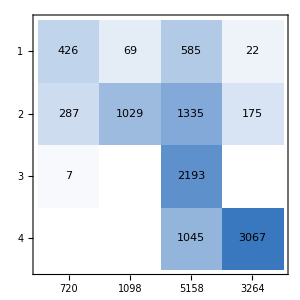
{0.655762,<|1→0.591667,2→0.937158,3→0.425165,4→0.939645|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA11, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA11[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA11[highEntBigC]]
Thread[lowEntBigC->netECA11[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

```mathematica
test4Data6kr1C11 = data6TC[8,200,120];
Thread[test4Data6kr1C11->netECA11[Keys@test4Data6kr1C11,{"TopProbabilities",2}]]
```

{(-Graphics-→1419281358352)→{4→0.00602441,3→0.99389},(-Graphics-→2064444354689)→{4→0.0212868,3→0.978648},(-Graphics-→916596312254)→{4→0.0243022,3→0.969311},(-Graphics-→2039112081907)→{4→0.00169424,3→0.997104},(-Graphics-→2149512300380)→{4→0.00372277,3→0.996249},(-Graphics-→2566332989862)→{2→0.0756346,4→0.899696},(-Graphics-→676389607350)→{2→0.0321344,4→0.941613},(-Graphics-→2740690847079)→{2→0.00555282,4→0.994224}}

```mathematica
test4Data5kr1C11 = data5T2C[8,200,120];
Thread[test4Data5kr1C11->netECA11[Keys@test4Data5kr1C11,{"TopProbabilities",2}]]
```

{(-Graphics-→253321705)→{3→0.0406888,4→0.959258},(-Graphics-→196492476)→{3→0.319759,4→0.532228},(-Graphics-→788955099)→{4→0.0648139,3→0.932434},(-Graphics-→1103573646)→{3→0.24185,4→0.755695},(-Graphics-→547423305)→{3→0.0231339,4→0.970644},(-Graphics-→583238302)→{3→0.00385114,4→0.992991},(-Graphics-→12037258)→{4→0.0081187,3→0.991747},(-Graphics-→554494784)→{2→0.00896273,4→0.982787}}

### Network XII - Two convolutions, dropout on linear only, BatchNorm

```mathematica
netECA12=netSevenCC512drop[200,120]
```

NetChain[<>]

```mathematica
NetInformation[netECA12,"MXNetNodeGraphPlot"]
```

-Graphics-

```mathematica
NetInformation[netECA12,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA12=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC12=genData2r2C[200,120,1024];
```

```mathematica
dataTotalistic3BigC12=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC12=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC12=genData5TCC[200,120,4096];
```

```mathematica
fullTrainingBigC12=Join[dataECA12,dataTotalistic2BigC12,dataTotalistic3BigC12,dataTotalistic4BigC12,dataTotalistic5BigC12];
Length[fullTrainingBigC12]
```

```mathematica
RandomSample[fullTrainingBigC12,20]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA12=NetTrain[netECA12,fullTrainingBigC12,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network XII

```mathematica
testDataECABigC=dataC[200,120,1024];
testData2TBigC=genData2r2C[200,120,1024];
testData3TBigC=data3T2C[200,120,1024];
testData4TBigC=data4TC[200,120,1024];
testData5TBigC=genData5TCC[200,120,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4}

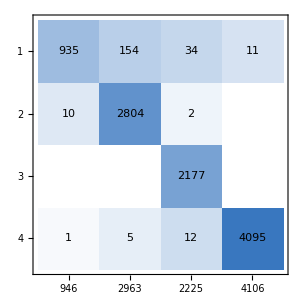
{0.977637,<|1→0.988372,2→0.946338,3→0.978427,4→0.997321|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA12, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

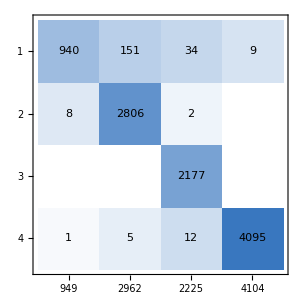
{0.97832,<|1→0.990516,2→0.947333,3→0.978427,4→0.997807|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA12, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA12[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA12[highEntBigC]]
Thread[lowEntBigC->netECA12[lowEntBigC]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→4}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4}

```mathematica
test4Data2kr2C12 = datak2r2C[200,120,8];
Thread[test4Data2kr2C12->netECA12[Keys@test4Data2kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→3810186600)→{4→0.180333,3→0.694341},(-Graphics-→839384167)→{4→0.202548,3→0.710777},(-Graphics-→4083057627)→{4→0.0465549,2→0.943023},(-Graphics-→37059758)→{4→0.0610776,3→0.903519},(-Graphics-→19082899)→{3→0.180083,2→0.766989},(-Graphics-→4251088224)→{1→0.107157,2→0.786419},(-Graphics-→520672316)→{3→0.192059,4→0.764214},(-Graphics-→4137587323)→{3→0.0240286,2→0.96822}}

```mathematica
test4Data3kr2C12 = datak3r2C[200,120,8];
Thread[test4Data3kr2C12->netECA12[Keys@test4Data3kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→57888)→{3→0.000319648,4→0.999677},(-Graphics-→15992)→{3→0.0159007,4→0.984093},(-Graphics-→127256)→{3→0.0064381,4→0.993557},(-Graphics-→82194)→{2→0.30342,3→0.480441},(-Graphics-→121955)→{4→0.0876676,3→0.911804},(-Graphics-→18609)→{3→0.0292597,4→0.956262},(-Graphics-→80523)→{1→0.0255402,4→0.944271},(-Graphics-→17158)→{3→0.219209,4→0.780559}}

```mathematica
test4Data3kr3C12 = datak3r3C[200,120,8];
Thread[test4Data3kr3C12->netECA12[Keys@test4Data3kr3C12,{"TopProbabilities",2}]]
```

{(-Graphics-→8165779)→{4→0.155419,3→0.844481},(-Graphics-→8260571)→{2→0.096984,4→0.865267},(-Graphics-→12907242)→{3→0.0715551,4→0.928399},(-Graphics-→4200129)→{2→0.047994,3→0.922454},(-Graphics-→3720629)→{4→0.180184,3→0.706124},(-Graphics-→11381083)→{3→0.11831,4→0.88157},(-Graphics-→3792153)→{3→0.123683,4→0.875272},(-Graphics-→3917135)→{3→0.0917601,4→0.90816}}

```mathematica
test4Data4kr2C12 = datak4r2C[200,120,8];
Thread[test4Data4kr2C12->netECA12[Keys@test4Data4kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→2224781264)→{3→0.0285837,4→0.971019},(-Graphics-→2473637100)→{3→0.0119387,4→0.985107},(-Graphics-→1981516373)→{3→0.0956149,4→0.904368},(-Graphics-→236606638)→{3→0.0850797,4→0.907215},(-Graphics-→3311938140)→{3→0.108194,4→0.891793},(-Graphics-→4114370215)→{3→0.0882479,4→0.911645},(-Graphics-→170189180)→{4→0.227049,3→0.766198},(-Graphics-→1987371238)→{3→0.0417003,4→0.958277}}

```mathematica
test4Data5kr1C12 = data5T2C[8,200,120];
Thread[test4Data5kr1C12->netECA12[Keys@test4Data5kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→542624083)→{3→0.0105002,4→0.986288},(-Graphics-→1220113097)→{2→0.0251884,4→0.974702},(-Graphics-→558087731)→{4→0.467576,3→0.53188},(-Graphics-→262964621)→{1→0.0089634,3→0.985923},(-Graphics-→730978099)→{3→0.157808,4→0.811715},(-Graphics-→791590316)→{2→0.0929642,4→0.858668},(-Graphics-→688665106)→{3→0.0983378,4→0.889688},(-Graphics-→972223099)→{3→0.00485827,4→0.994969}}

```mathematica
test4Data5kr1C12 = data5T2C[8,200,120];
Thread[test4Data5kr1C12->netECA12[Keys@test4Data5kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→615859649)→{4→0.00300542,3→0.996675},(-Graphics-→667253917)→{3→0.267714,4→0.666951},(-Graphics-→186716302)→{3→0.0406313,4→0.948739},(-Graphics-→900872906)→{2→0.0400835,4→0.940853},(-Graphics-→1010285849)→{3→0.129844,4→0.867114},(-Graphics-→233853421)→{4→0.336261,3→0.663526},(-Graphics-→419602348)→{4→0.114922,3→0.884835},(-Graphics-→466483737)→{3→0.210458,4→0.781966}}

```mathematica
test4Data5kr1C12 = data5T2C[8,200,120];
Thread[test4Data5kr1C12->netECA12[Keys@test4Data5kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→641263827)→{3→0.00662468,4→0.993323},(-Graphics-→264450009)→{2→0.00554177,3→0.990993},(-Graphics-→1139267024)→{3→0.290709,4→0.707738},(-Graphics-→1002452740)→{2→0.0828806,3→0.908103},(-Graphics-→710356086)→{4→0.464106,3→0.535843},(-Graphics-→699026697)→{3→0.0290606,4→0.970822},(-Graphics-→162408030)→{4→0.127347,3→0.871877},(-Graphics-→854884391)→{3→0.187553,4→0.808008}}

```mathematica
test4Data6kr1C12 = data6TC[8,200,120];
Thread[test4Data6kr1C12->netECA12[Keys@test4Data6kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→223166858977)→{4→0.208566,3→0.789881},(-Graphics-→101119403496)→{3→0.138136,4→0.859864},(-Graphics-→2753334309735)→{3→0.178436,4→0.819991},(-Graphics-→2638229466672)→{3→0.00411566,4→0.995873},(-Graphics-→220191931566)→{3→0.00383046,4→0.996144},(-Graphics-→1354199697456)→{3→0.096483,4→0.882998},(-Graphics-→2517198152824)→{4→0.242152,3→0.757815},(-Graphics-→342239140319)→{4→0.124124,3→0.874294}}

```mathematica
test4Data6kr1C12 = data6TC[8,200,120];
Thread[test4Data6kr1C12->netECA12[Keys@test4Data6kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→759596687358)→{3→0.167841,4→0.832159},(-Graphics-→762192153436)→{4→0.484578,3→0.511697},(-Graphics-→368289908645)→{4→0.0364979,3→0.963421},(-Graphics-→952948862533)→{3→0.215139,4→0.784821},(-Graphics-→1720850295450)→{4→0.00014493,3→0.999851},(-Graphics-→2759945912780)→{3→0.00984137,4→0.990158},(-Graphics-→762235461409)→{4→0.0047512,3→0.995249},(-Graphics-→1589235078435)→{3→0.161045,4→0.833715}}

```mathematica
test4Data6kr2C12 = data6T2C[8,200,120];
Thread[test4Data6kr2C12->netECA12[Keys@test4Data6kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→27148559305859136233)→{4→0.0471847,3→0.952814},(-Graphics-→109406220086847849858)→{4→0.0899908,3→0.895993},(-Graphics-→26205502254809163684)→{3→0.405219,4→0.594381},(-Graphics-→86427159345288879260)→{3→0.0689922,4→0.930986},(-Graphics-→107181556735757281654)→{4→0.270156,3→0.720175},(-Graphics-→45409684118792977329)→{4→0.356656,3→0.643203},(-Graphics-→149752836095638129253)→{4→0.479288,3→0.520519},(-Graphics-→156570576117400139756)→{3→0.128028,4→0.870806}}

```mathematica
test4Data6kr2C12 = data6T2C[8,200,120];
Thread[test4Data6kr2C12->netECA12[Keys@test4Data6kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→109870782757791541134)→{3→0.135194,4→0.864332},(-Graphics-→101763778526350204910)→{4→0.299111,3→0.700889},(-Graphics-→168191446633249217669)→{3→0.168579,4→0.830329},(-Graphics-→58178996181206996350)→{3→0.0377213,4→0.962275},(-Graphics-→151368347284185302744)→{4→0.21601,3→0.783986},(-Graphics-→148083457264742949838)→{3→0.0301855,4→0.969694},(-Graphics-→31243373638727836633)→{3→0.0467683,4→0.95323},(-Graphics-→142675060537710875008)→{4→0.433908,3→0.562452}}

```mathematica
test4Data6kr2C12 = data6T2C[8,200,120];
Thread[test4Data6kr2C12->netECA12[Keys@test4Data6kr2C12,{"TopProbabilities",2}]]
```

{(-Graphics-→147738617724518164282)→{3→0.27497,4→0.725025},(-Graphics-→73594928115534548004)→{4→0.385864,3→0.613928},(-Graphics-→66722584087999263242)→{3→0.269977,4→0.723808},(-Graphics-→10352263934892128786)→{3→0.0454232,4→0.946219},(-Graphics-→22141296065668104577)→{4→0.239737,3→0.756623},(-Graphics-→120088379496541826693)→{4→0.484884,3→0.515109},(-Graphics-→70970883824344324110)→{3→0.000347619,4→0.999651},(-Graphics-→107036672584028279663)→{4→0.372753,3→0.627107}}

```mathematica
test4Data7kr1C12 = data7TC[8,200,120];
Thread[test4Data7kr1C12->netECA12[Keys@test4Data7kr1C12,{"TopProbabilities",2}]]
```

{(-Graphics-→8390463346708863)→{3→0.499036,4→0.500696},(-Graphics-→10800146574675822)→{3→0.321906,4→0.663144},(-Graphics-→8847467037462318)→{4→0.0905919,3→0.909297},(-Graphics-→3927833926157736)→{4→0.000449315,3→0.999551},(-Graphics-→6899982827499026)→{3→0.480662,4→0.519338},(-Graphics-→4095053468931771)→{4→0.00260853,3→0.997391},(-Graphics-→7294598776620303)→{4→0.0000304245,3→0.999969},(-Graphics-→6250398685738367)→{4→0.445247,3→0.554743}}

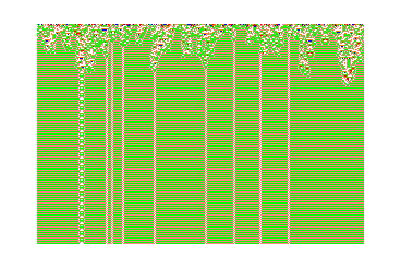

```mathematica
RulePlot[CellularAutomaton[{762192153436,{6,1},1}],RandomInteger[5,300],200,PlotLegends->"Icon",ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple}]
```

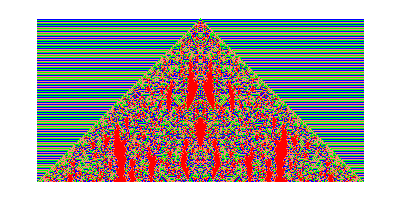

```mathematica
RulePlot[CellularAutomaton[{2759945912780,{6,1},1}],{{3},0},200,PlotLegends->"Icon",ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple}]
```

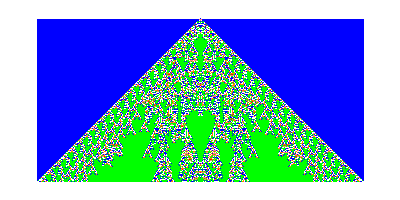

```mathematica
RulePlot[CellularAutomaton[{1826899946618,{6,1},1}],{{2},0},200,PlotLegends->"Icon",ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple}]
```

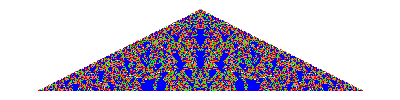

```mathematica
RulePlot[CellularAutomaton[{70970883824344324110,{6,1},2}],{{1},0},200,PlotLegends->"Icon",ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple}]
```

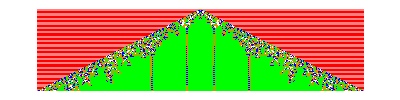

```mathematica
RulePlot[CellularAutomaton[{31243373638727836633,{6,1},2}],{{1},0},200,PlotLegends->"Icon",ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple}]
```

### Generate test data for Network IV

```mathematica
testDataECABigC=dataC[200,120,2048];
testData3TBigC=data3T2C[200,120,2048];
testData4TBigC=data4TC[200,120,2048];
testData5TBigC=data5T4C[2048,200,120];
fullTestSetBigC=Join[testDataECABigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

8192

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
NetMeasurements[netECA4,fullTestSetBigC,{"Accuracy","Precision","Recall"}]
```

{0.871094,<|1→0.865385,2→0.87123,3→0.176707,4→1.|>,<|1→0.491803,2→0.977228,3→0.651852,4→0.865527|>}

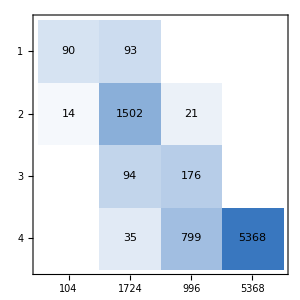
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[netECA4,fullTestSetBigC,"ConfusionMatrixPlot"]
```

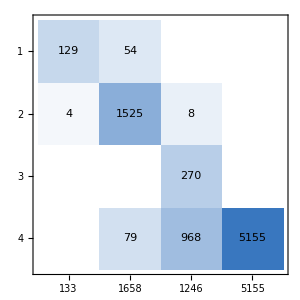
{0.864136,<|1→0.969925,2→0.919783,3→0.216693,4→1.|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA5, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

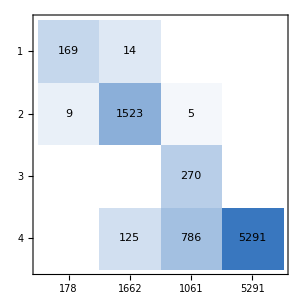
{0.885376,<|1→0.949438,2→0.916366,3→0.254477,4→1.|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA6, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

### Checking highest- and lowest-entropy images in test set for Network IV

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA4[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]]
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC->netECA4[highEntBigC]]
Thread[lowEntBigC->netECA4[lowEntBigC]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking Entropy for Network V

```mathematica
entropyImagesBigC5=RandomSample[Keys[fullTestSetBigC],2000];
entropiesBigC5=netECA5[entropyImagesBigC5,"Entropy"];
highEntBigC5=entropyImagesBigC5[[Ordering[entropiesBigC5,-10]]]
lowEntBigC5=entropyImagesBigC5[[Ordering[entropiesBigC5,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC5->netECA5[highEntBigC5]]
Thread[lowEntBigC5->netECA5[lowEntBigC5]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking Entropy for Network VI

```mathematica
entropyImagesBigC6=RandomSample[Keys[fullTestSetBigC],2000];
entropiesBigC6=netECA6[entropyImagesBigC6,"Entropy"];
highEntBigC6=entropyImagesBigC6[[Ordering[entropiesBigC6,-10]]]
lowEntBigC6=entropyImagesBigC6[[Ordering[entropiesBigC6,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC6->netECA6[highEntBigC6]]
Thread[lowEntBigC6->netECA6[lowEntBigC6]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4}

### Testing Network IV on k=5/6, r=1 images

```mathematica
netECA4=Import["netECA4-22may-3.wlnet","WLNet"]
```

NetChain[<>]

```mathematica
testData5kr1C=data5T2C[10,200,120];
k5r1testC=Thread[testData5kr1C->netECA4[Keys@testData5kr1C]]
```

{(-Graphics-→555274587)→2,(-Graphics-→830440453)→2,(-Graphics-→256015586)→2,(-Graphics-→602299808)→3,(-Graphics-→537138645)→3,(-Graphics-→1018759951)→3,(-Graphics-→1183999995)→2,(-Graphics-→656480350)→3,(-Graphics-→275099445)→3,(-Graphics-→727878792)→3}

```mathematica
testData6kr1C = data6TC[10,200,120];
k6r1testC=Thread[testData6kr1C->netECA4[Keys@testData6kr1C]]
```

{(-Graphics-→1369280495157)→2,(-Graphics-→695147763153)→3,(-Graphics-→230820111692)→2,(-Graphics-→1786908954663)→3,(-Graphics-→1721005408527)→4,(-Graphics-→1876955187335)→3,(-Graphics-→2784813723143)→3,(-Graphics-→2435317049084)→3,(-Graphics-→1363396903494)→3,(-Graphics-→244892860791)→3}

### Testing network V on k=5/6, r=1 images

```mathematica
testData5kr1C5=data5T2C[20,200,120];
k5r1testC5=Thread[testData5kr1C5->netECA5[Keys@testData5kr1C5,{"TopProbabilities",2}]]
```

{(-Graphics-→648626494)→{2→0.0899356,4→0.907522},(-Graphics-→36969296)→{3→0.234358,4→0.765633},(-Graphics-→1164564486)→{4→0.000149515,3→0.99985},(-Graphics-→968895016)→{3→0.151381,4→0.848617},(-Graphics-→1041243317)→{4→0.0000845454,3→0.999913},(-Graphics-→679678365)→{3→0.0743836,2→0.901006},(-Graphics-→662375822)→{4→0.00157124,3→0.998327},(-Graphics-→622524470)→{3→0.37217,2→0.439608},(-Graphics-→310548859)→{3→0.1657,4→0.83423},(-Graphics-→381985281)→{2→0.204319,4→0.795246},(-Graphics-→155701712)→{4→0.145092,3→0.854907},(-Graphics-→514511817)→{4→0.0777484,2→0.916331},(-Graphics-→610750963)→{2→0.0018545,4→0.99744},(-Graphics-→97274978)→{4→0.00194351,2→0.997739},(-Graphics-→1081515933)→{2→0.00497279,4→0.995},(-Graphics-→101707725)→{4→0.388398,3→0.611587},(-Graphics-→593680512)→{4→0.000306886,3→0.999529},(-Graphics-→777716689)→{3→0.279784,4→0.71969},(-Graphics-→497757880)→{3→0.0234419,4→0.976438},(-Graphics-→364102552)→{4→0.0343015,2→0.96568}}

```mathematica
testData6kr1C5 = data6TC[20,200,120];
k6r1testC5=Thread[testData6kr1C5->netECA5[Keys@testData6kr1C5,{"TopProbabilities",2}]]
```

{(-Graphics-→2140322472981)→{4→0.385685,3→0.614177},(-Graphics-→2393914643526)→{4→0.0210504,3→0.978483},(-Graphics-→2053201776355)→{3→0.163982,2→0.714814},(-Graphics-→752141048566)→{4→0.107666,3→0.892334},(-Graphics-→1633214012187)→{3→0.256557,4→0.743419},(-Graphics-→205987104993)→{2→0.117551,4→0.882448},(-Graphics-→1677728204097)→{4→5.64455×10^-6,3→0.999994},(-Graphics-→2107263754397)→{4→0.082527,3→0.917473},(-Graphics-→1930003590251)→{4→0.106348,3→0.89365},(-Graphics-→2389529132771)→{3→0.00768888,4→0.992307},(-Graphics-→1709821319577)→{4→0.0175132,3→0.982487},(-Graphics-→1034507802034)→{2→0.35561,4→0.64424},(-Graphics-→1192465516957)→{3→0.0268969,4→0.970458},(-Graphics-→2661787172664)→{4→0.0404416,3→0.959429},(-Graphics-→847748942279)→{4→0.0713072,2→0.927012},(-Graphics-→1032388414942)→{4→0.00969077,3→0.990309},(-Graphics-→1666004891517)→{4→6.70879×10^-6,3→0.999993},(-Graphics-→2478541394776)→{4→0.277771,3→0.690083},(-Graphics-→932645253063)→{3→0.207994,4→0.792006},(-Graphics-→337558272813)→{4→0.134153,3→0.865846}}

### Testing network VI on k=5/6, r=1 images

```mathematica
testData5kr1C6=data5T2C[20,200,120];
k5r1testC6=Thread[testData5kr1C6->netECA6[Keys@testData5kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→57818283)→{4→0.0000238117,2→0.999973},(-Graphics-→1044867935)→{4→3.3046×10^-6,2→0.999997},(-Graphics-→480340855)→{2→0.0943981,4→0.891295},(-Graphics-→1108453625)→{4→2.68196×10^-9,2→1.},(-Graphics-→1188797638)→{4→0.44402,3→0.55598},(-Graphics-→194226008)→{4→0.209606,3→0.787397},(-Graphics-→750353946)→{4→0.0625052,3→0.937488},(-Graphics-→971654562)→{3→0.000554937,2→0.999},(-Graphics-→780837716)→{2→0.000975013,4→0.998843},(-Graphics-→1068887710)→{3→0.214754,4→0.782422},(-Graphics-→409160639)→{3→0.000406241,4→0.999593},(-Graphics-→64616370)→{4→0.203775,3→0.795874},(-Graphics-→935443699)→{2→0.00526674,4→0.994731},(-Graphics-→655296617)→{3→0.0666499,4→0.933317},(-Graphics-→693095807)→{4→0.149592,3→0.850377},(-Graphics-→950965544)→{4→0.137234,2→0.859277},(-Graphics-→565424043)→{4→0.336171,2→0.661287},(-Graphics-→265460035)→{4→0.440836,3→0.559164},(-Graphics-→942021430)→{3→0.0994604,2→0.900525},(-Graphics-→319713877)→{3→0.186876,4→0.813122}}

```mathematica
testData6kr1C6 = data6TC[20,200,120];
k6r1testC6=Thread[testData6kr1C6->netECA6[Keys@testData6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1207010117645)→{4→0.00831573,3→0.991479},(-Graphics-→322146672175)→{2→0.0748844,4→0.92511},(-Graphics-→2608753185152)→{3→0.168331,4→0.790787},(-Graphics-→2592706257887)→{4→0.0294994,3→0.9705},(-Graphics-→1053338235394)→{4→0.178319,3→0.818732},(-Graphics-→1044114503140)→{4→0.0410611,3→0.958927},(-Graphics-→564898470856)→{4→0.0359682,3→0.964014},(-Graphics-→2666816750422)→{3→0.0384538,4→0.961546},(-Graphics-→2743020733306)→{2→0.0124328,4→0.986006},(-Graphics-→1661403844932)→{2→0.0980948,3→0.895002},(-Graphics-→1941732867200)→{3→0.0000540623,4→0.999946},(-Graphics-→1931468347465)→{4→0.431502,3→0.560876},(-Graphics-→1190433074497)→{2→0.00265841,4→0.997045},(-Graphics-→2308189821626)→{4→0.113693,3→0.884634},(-Graphics-→18345165990)→{2→0.122598,3→0.820363},(-Graphics-→1214767416307)→{3→0.00107258,4→0.998335},(-Graphics-→972231004329)→{4→0.128884,3→0.871115},(-Graphics-→1459828799229)→{3→0.0429323,4→0.934185},(-Graphics-→1613375044836)→{3→0.221142,4→0.778858},(-Graphics-→226868632354)→{4→0.22783,3→0.77217}}

```mathematica
tempNet1=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}]
newNet1=NetChain[<|"pretrainedNet"->tempNet1,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",Range[1,4]}]]
trainedNet1=NetTrain[newNet1,fullTrainingBigC3,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<>]

NetChain[<>]

NetChain[<>]